```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/poslavsky/Library/Containers/com.apple.mail/Data/Library/Mail Downloads/6677D6F6-6E56-4370-B817-3060F87F0F13/check

```mathematica
(*PrependTo[$Path,"/home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg"];*)
```

```mathematica
<<X`
```

Package-X v1.0.4, by Hiren H. Patel

For more information, see the

```mathematica
NumericQ[r]=True;
```

```mathematica
PackageXSubs={LDot[p3,p3]->m^2,LDot[p4,p4]->m^2,LDot[p3,p4]->s/2-m^2,mc-> r m, mb-> (1-r) m};
```

```mathematica
toABC={pvA[a_,b_]:>A[b],pvB[a_,b_,c___]:>B[c],pvC[a_,b_,c_,d___]:>C[d],pvC0[a__]:>C[a]};
topvABC={A[a_]:>pvA[0,a],B[a__]:>pvB[0,0,a],C[a__]:>pvC[0,0,0,a]};
```

```mathematica
factor=(Exp[EulerGamma] 1/(4 Pi))^-eps
```

ⅇ^(ℽ (-eps)) (4 π)^eps

```mathematica
ff=Gamma[1-2 eps]/(Gamma[1-eps]^2 Gamma[1+eps](4 Pi)^eps I/(16 Pi^2))
```

-(ⅈ (4 π)^(2-eps) 1-2 eps)/((1-eps)^2 eps+1)

```mathematica
invff=1/ff
```

(ⅈ (4 π)^(eps-2) (1-eps)^2 eps+1)/(1-2 eps)

```mathematica
Normal[Series[FullSimplify[1/factor invff],{eps,0,1}]]
```

ⅈ/(16 π^2)

```mathematica
norm=Expand[Normal[Series[FullSimplify[1/factor invff],{eps,0,2}]]/(I/(16 Pi^2))]
```

1-(π^2 eps^2)/12

```mathematica
Fb=(((1-r)^2 m^2)/mmu)^-eps
```

((m^2 (1-r)^2)/mmu)^-eps

```mathematica
Fc=((r^2 m^2)/mmu)^-eps
```

((m^2 r^2)/mmu)^-eps

```mathematica
Fb=Plus@@ Factor[List@@ Normal[Series[Fb,{eps,0,1}]]/.{Log[(m^2 (1-r)^2)/mmu]->Log[m^2/mmu]+ 2 Log[1-r]}]
```

1-eps (log(m^2/mmu)+2 log(1-r))

```mathematica
Fc=Plus@@ Factor[List@@ Normal[Series[Fc,{eps,0,1}]]/.{Log[(m^2 r^2)/mmu]->Log[m^2/mmu]+ 2 Log[r]}]
```

1-eps (log(m^2/mmu)+2 log(r))

```mathematica
A0[m_]:=m^2+m^2/eps+eps*m^2+(eps*m^2*Pi^2)/6+m^2*Log[mmu/m^2]+eps*m^2*Log[mmu/m^2]+(eps*m^2*Log[mmu/m^2]^2)/2
```

```mathematica
F21[z_]:=(1-eps)/(2 (1-2 eps) z)(1+z-(1-z)^(1-2 eps)-2 (1-z)^(1-2 eps) eps (eps PolyLog[1,1,z]+Hui eps^2 Sum[(-2)^(j-k) PolyLog[k,3-k],{k,1,2}]))
```

```mathematica
B0polylog[s_,m1_,m2_]:=Block[{x,y,lam},If[m1≠ 0 && m2≠0,x=m1^2/s;y=m2^2/s;lam=√((1-x-y)^2-4 x y);  mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps ((Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps] lam^(1- 2 eps)-Gamma[-1+eps] 1/2(1+x-y-lam) (-x)^-eps F21[(1+x-y-lam)^2/(4 x)]-
Gamma[-1+eps] 1/2(1-x+y-lam) (-y)^-eps F21[(1-x+y-lam)^2/(4 y)]),If[m1==0 && m2 ≠ 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m2^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m2^2],If[m1≠ 0 && m2== 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m1^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m1^2],If[m1==0 && m2==0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps (Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps]]]]]]
```

```mathematica
<<cross-sectionNLOLarin.res
```

```mathematica
X[a_]:=norm
```

```mathematica
pow[a_,b_]:=a^b
```

```mathematica
andr[ecm_] := Block[{mc=1.3,mb=4,m=mc+mb,r=mc/m,CF=4/3,CA=3,pi=Pi,s=ecm^2,mt=170,R1=1,R2=1,AL=1/137,ex},

ex[1]=Collect[Expand[crosssection//N],{A[___],B[___],C[___]}];
ex[2]=Expand[Simplify[Normal[Series[ex[1]/.{A[m_]:> A0[m],B[s_,0.,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]],B[s_,m_,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]],B[s_,0.,m_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]],B[s_,m1_,m2_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]],Aconj[m_]:> Conjugate[A0[m]],Bconj[s_,0.,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]],Bconj[s_,m_,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]]],Bconj[s_,0.,m_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]]],Bconj[s_,m1_,m2_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]]],log[a_]:>  Log[a]},{eps,0,0}]]/.{Log[a_ mmu]-> Log[a]+Log[mmu]}]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}];
ex[3]=Expand[Chop[LoopRefine[Expand[Normal[Series[ex[2],{eps,0,0}]]/.{Cconj[a___]:> Conjugate[C[a]]}]/.topvABC],10^(-20)]];
ex[4]=Collect[Chop[ex[3],10^(-20)],AS]/.{AS-> z *0.3}//Expand;
ex[4]
]
```

```mathematica
andrEcmDep = Table[andr[e],{e,15.1047,25.1047,1}];
```

```mathematica
Table[e,{e,15.1047,25.1047,1}]
```

{15.1047,16.1047,17.1047,18.1047,19.1047,20.1047,21.1047,22.1047,23.1047,24.1047,25.1047}

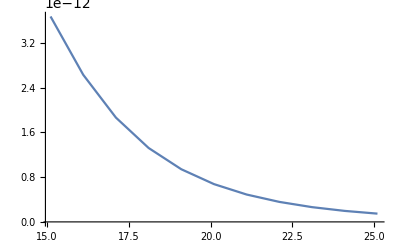

```mathematica
ListPlot[Transpose@{Table[e,{e,15.1047,25.1047,1}],#/.mmu->2 5.3/.z->1&/@andrEcmDep},Joined->True]
```

```mathematica
224455460
```

```mathematica
?FrobeniusSolve
```

FrobeniusSolve[{a_1,…,a_n},b] gives a list of all solutions of the Frobenius equation a_1 x_1+…+a_n x_n=b.
FrobeniusSolve[{a_1,…,a_n},b,m] gives at most m solutions.

```mathematica
FrobeniusSolve[{44177126,82307856,93818647,94838855},224455460]
```

{}

```mathematica
224455460-44177126
```

180278334

```mathematica
r3 = Block[{mc=1.3,mb=4,m=mc+mb,r=mc/m,CF=4/3,CA=3,pi=Pi,s=27.6047^2,mt=170,R1=1,R2=1,AL=1/137,ex},

ex[1]=Collect[Expand[crosssection//N],{A[___],B[___],C[___]}];
ex[2]=Expand[Simplify[Normal[Series[ex[1]/.{A[m_]:> A0[m],B[s_,0.,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]],B[s_,m_,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]],B[s_,0.,m_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]],B[s_,m1_,m2_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]],Aconj[m_]:> Conjugate[A0[m]],Bconj[s_,0.,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]],Bconj[s_,m_,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]]],Bconj[s_,0.,m_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]]],Bconj[s_,m1_,m2_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]]],log[a_]:>  Log[a]},{eps,0,0}]]/.{Log[a_ mmu]-> Log[a]+Log[mmu]}]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}];
ex[3]=Expand[Chop[LoopRefine[Expand[Normal[Series[ex[2],{eps,0,0}]]/.{Cconj[a___]:> Conjugate[C[a]]}]/.topvABC],10^(-20)]];
ex[4]=Collect[Chop[ex[3],10^(-20)],AS]/.{AS-> z *0.3}//Expand;
ex[4]
]
```

-4.91993×10^-14 z^3 log(mmu)+1.1754×10^-13 z^3+7.37879×10^-14 z^2

```mathematica
my1={49.888 ,57.159};
my2 = {3.7787 ,4.6933};
my3 = {0.8728 ,1.1365};
```

```mathematica
(Coefficient[#/.mmu->2 5.3,z,2]&/@{r1,r2,r3})/(#⟦1⟧&/@{my1,my2,my3})
```

{8.45393×10^-14,8.45411×10^-14,8.45416×10^-14}

```mathematica
(Coefficient[#/.mmu->2 5.3,z,3]&/@{r1,r2,r3})/(#⟦2⟧&/@{my1,my2,my3})
```

{-9.50717×10^-15,-2.7209×10^-15,1.2209×10^-15}

```mathematica
#/.mmu->2 5.3/.z->1&/@{r1,r2,r3}
```

{3.67407×10^-12,3.06685×10^-13,7.51755×10^-14}

```mathematica
r1/.mmu->2 5.3
```

4.21749×10^-12 z^2-5.4342×10^-13 z^3

```mathematica
Expand[0.3894 10^12 ex[4]/.mmu->2m]
```

1.64229 z^2-0.211608 z^3

```mathematica
ratioCrossSection[mu2_]:=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]/.{mmu-> mu2}]]
```

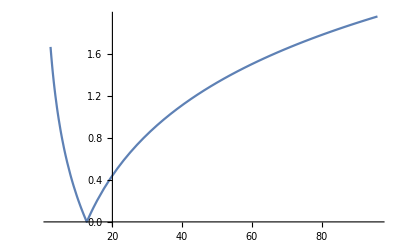

```mathematica
Plot[ratioCrossSection[mmu],{mmu,(mc)^2,(2mb)^2}]
```

```mathematica
ratioCrossSection[(2mc)^2]
```

0.328113

```mathematica
CrossSectionRatio=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]]]/.{mmu-> m^2}
```

1.13273

```mathematica
Chop[Expand[ex[4]0.3894 10^12/.{mmu-> (2 mc)^2}],10^(-9)]
```

0.300527 z^3+0.915924 z^2